```mathematica
Nx=15;
Ny=15;
nx=15;
ny=15;
datrotuwsoca=Flatten[Import["trot_0.4_nutcalca.dat"]];
datrotdwsoca=Flatten[Import["trot_0.4_ndtcalca.dat"]];
datrotuwsocb=Flatten[Import["trot_0.4_nutcalcb.dat"]];
datrotdwsocb=Flatten[Import["trot_0.4_ndtcalcb.dat"]];
```

```mathematica
impdiffdata=Table[Partition[(datrotuwsoca+datrotdwsoca),3][[i,1]] + Partition[(datrotuwsoca+datrotdwsoca),3][[i,2]]+ Partition[(datrotuwsoca+datrotdwsoca),3][[i,3]],{i,1,Nx*Ny}];

diffdata=impdiffdata;
```

```mathematica
impdiffdatb=Table[Partition[(datrotuwsocb+datrotdwsocb),3][[i,1]] + Partition[(datrotuwsocb+datrotdwsocb),3][[i,2]]+ Partition[(datrotuwsocb+datrotdwsocb),3][[i,3]],{i,1,Nx*Ny}];

diffdatb=impdiffdatb;
```

```mathematica
plotdiffdata=Partition[Riffle[diffdata,Table[0,{i,Length[diffdata]}]],2*Sqrt[Length[diffdata]]];
plotdiffdatb=Partition[Riffle[Table[0,{i,Length[diffdatb]}],diffdatb],2*Sqrt[Length[diffdatb]]];
plotdiffdatab=Riffle[plotdiffdata,plotdiffdatb];
```

```mathematica
length=Sqrt[Length[diffdata]];
hlength=IntegerPart[length/2];
```

```mathematica
l=0;
For[i=1,i<=nx,i++,
For[j=1,j<=ny,j++,
xpos=(j-1) - (i - 1);
ypos=(j-1) + (i - 1);
l = l+1;
coorda[l] = {xpos,ypos};
];];
l=0;
For[i=1,i<=nx,i++,
For[j=1,j<=ny,j++,
xpos=(j-1) - (i - 1);
ypos=(j-1) + (i - 1)+1;
l = l+1;
coordb[l] = {xpos,ypos};
];];
rownumber=7;
countatom=7;

midatom=(nx*rownumber + countatom)+1;
midcoord=coorda[midatom];
```

```mathematica
For[l=1,l<=nx*ny,l++,
newcoorda[l] = coorda[l] - midcoord];
For[l=1,l<=nx*ny,l++,
newcoordb[l] = coordb[l] - midcoord];

ndiffdata = Table[Flatten[{newcoorda[l] ,diffdata[[l]]}],{l,1,nx*ny}];
ndiffdatb = Table[Flatten[{newcoordb[l] ,diffdatb[[l]]}],{l,1,nx*ny}];
```

```mathematica
alldiffdata= Join[ndiffdata ,ndiffdatb ];
limval = alldiffdata[[All,3]];
minval=3.96;
maxval=3.99;
```

```mathematica
squarelength=5;
xmax=squarelength;
xmin=-squarelength;
ymax=squarelength;
ymin=-squarelength;

posmidcoord = {0,0};
coordx1 = xmin;
coordy1 = ymin;
coordx2 = xmax;
coordy2 = ymin;
coordx3 = xmax;
coordy3 = ymax;
coordx4 = xmin;
coordy4 = ymax;

squareline=
{Blue,Thickness[0.01],Line[{{{coordx1,coordy1},{coordx2,coordy2}},{{coordx2,coordy2},{coordx3,coordy3}},{{coordx3,coordy3},{coordx4,coordy4}},{{coordx4,coordy4},{coordx1,coordy1}}}]};
slcoordx1=0.5;
slcoordy1=2.5;
slcoordx2=-2.5;
slcoordy2=-0.5;
slcoordx3=-0.5;
slcoordy3=-2.5;
slcoordx4=2.5;
slcoordy4=0.5;
slsquareline=
{Black,Dashed,Thickness[0.015],Line[{{{slcoordx1,slcoordy1},{slcoordx2,slcoordy2}},{{slcoordx2,slcoordy2},{slcoordx3,slcoordy3}},{{slcoordx3,slcoordy3},{slcoordx4,slcoordy4}},{{slcoordx4,slcoordy4},{slcoordx1,slcoordy1}}}]};
```

```mathematica
rmvpoints1=DeleteCases[Table[If[alldiffdata[[i,1]]>coordx3,pt=Null,If[alldiffdata[[i,2]]>coordy3,pt=Null,pt={alldiffdata[[i,1]],alldiffdata[[i,2]],alldiffdata[[i,3]]}]];pt,{i,1,Length[alldiffdata]}],Null];

rmvpoints2=DeleteCases[Table[If[rmvpoints1[[i,1]]<coordx1,pt=Null,If[rmvpoints1[[i,2]]<coordy1,pt=Null,pt={rmvpoints1[[i,1]],rmvpoints1[[i,2]],rmvpoints1[[i,3]]}]];pt,{i,1,Length[rmvpoints1]}],Null];
```

```mathematica
slimval=rmvpoints2[[All,3]];
sminval=3.92;
smaxval=4;
spointlegend=BarLegend[{"Rainbow",{sminval,smaxval}},LabelStyle->{FontFamily->"TimesNewRoman",Directive[Black,24]}];
```

```mathematica
avval=(smaxval+sminval)/2;
ftrmvpoints2=Table[If[sminval>=rmvpoints2[[i,3]],pt={rmvpoints2[[i,1]],rmvpoints2[[i,2]],(sminval-avval)},If[smaxval<=rmvpoints2[[i,3]],pt={rmvpoints2[[i,1]],rmvpoints2[[i,2]],(smaxval-avval)},pt={rmvpoints2[[i,1]],rmvpoints2[[i,2]],(rmvpoints2[[i,3]]-avval)}]],{i,1,Length[rmvpoints2]}];
```

```mathematica
k1max=100;
k2max=100;


For[k1=-k1max/2,k1≤k1max/2,k1++,
For[k2=-k2max/2,k2≤k2max/2,k2++,
kx=2Pi*k1/(k1max);
ky=2Pi*k2/(k2max);
mdiffdat=0;
For[i=1,i≤Length[ftrmvpoints2],i++,
mdiffdat=mdiffdat+ftrmvpoints2[[i,3]]*(Exp[I*(kx*ftrmvpoints2[[i,1]]+ky*ftrmvpoints2[[i,2]])])];
mdiff[k1,k2]=mdiffdat;]]
```

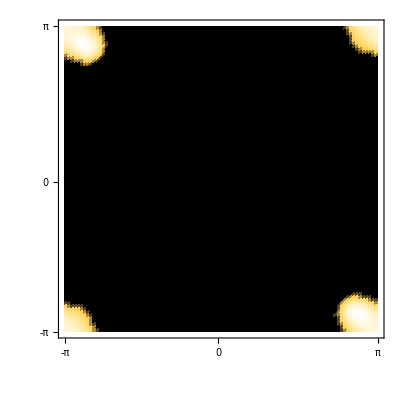

```mathematica
Clear[b,x]
nonorthleg=BarLegend["SunsetColors",LabelStyle->{Black,24}];
b1=ListDensityPlot[SetAccuracy[(1.8)Table[Abs[mdiff[k1,k2]],{k2,-k2max/2,k2max/2},{k1,-k1max/2,k1max/2}],0],PlotRange->All,
LabelStyle->{FontFamily->"TimesNewRoman",Directive[Black,24]},
PlotRangeClipping -> False,
FrameTicks->{{{{1,"-π"},{k1max/2,"0"},{k1max+1,"π"}},{{1,Null},{k1max/2,Null},{k1max+1,Null}}},{{{1,"-π"},{k2max/2,"0"},{k2max+1,"π"}},{{1,Null},{k2max/2,Null},{k2max+1,Null}}}},
FrameTicksStyle->Directive[FontFamily->"TimesNewRoman",Black,25],
Epilog -> {Rotate[Text[Style[Subscript[K,y],25],{-12,50.7}],Pi/2],Text[Style[Subscript[K,x],25],{50, -15}]},ImagePadding->{{49,15},{65,17}},
ColorFunction->"SunsetColors",ImageSize->400]         
Export["charge_ordering_momentum_space.png",b1];
```